# Unit 4 Notes

## Chapter 8

8.1 Arc Length

## Preview:

## Theory pt1:

## Relevant Equations:

```mathematica
-Graphics-
arcLengthforContinousFx = ∫_a^b √(1+(F'[x_])^2)ⅆx
-Graphics-
arcLengthforContinousFy = ∫_a^b √(1+(G'[y_])^2)ⅆy
```

## Example 1:

```mathematica
(* Find the length of the arc of the semicubical parabola *)
y^2=x^3;
(*step 2 -> graph f(x)*)
```

```mathematica
ContourPlot[x^3 == y^2, {x, -1.7, 4}, {y, -1.7, 8}]
```

```mathematica
-Graphics-
(*  (*The length of the arc from the redline to the top of the curve*)
```

```mathematica
F[x_] := √(x^3);
F'[x_] := (3 x^2)/(2 √(x^3))
∫_1^4 √(1+(9x)/4)ⅆx
u= 1 + 9/4 x
4/3 ⅆu=ⅆx
4/3∫_1^4 u^(1/2)ⅆu = (8 u^(3/2))/9 = (8(1 + 9/4 x)^(3/2))/9{A=1; B=4} (*int b-a*)
```

```mathematica
∫_1^4 √(1+(9x)/4)ⅆx
```

```mathematica
Subscript[Arc, L]=1/27 (80 √10-13 √13);
N[Subscript[Arc, L]]
```

7.63371

## Example 2:

```mathematica
Plot[Sqrt[2 - x^2], {x, -2.2, 2.2}]
```

```mathematica
(*Find the exact length of the curve point [a to b] *)
G[x_] :=√(2-x^2);
G'[x_] :=x/(√(2-x^2))
(* 0⩽x⩽1 *)
∫_a^b √(1+x^2/(2-x^2))ⅆx
```

```mathematica
Simplify[1+x^2/(2-x^2)]
```

-2/(-2+x^2)

```mathematica
-2∫_0^1 √(1/(x^2-2))ⅆx
```

```mathematica
∫_0^1 √(1+x^2/(2-x^2))ⅆx
```

```mathematica
Subscript[Arc, 1]=π/(2 √2) (* ArcLength of curve from 0 to 1 *)
N[Subscript[Arc, 1]]
```

1.11072

## Example 3:

```mathematica
(*Find the length of the curve *)
Z[x_] := √(64(x+1)^3) (* 0⩽x⩽3 *)
D[Z[x],x]
```

```mathematica
Plot[8*Sqrt[(1 + x)^3], {x, -2.6, 0.56}]
```

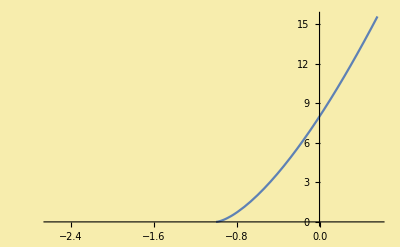

```mathematica
Show[%28,Background->RGBColor[0.97,0.93,0.68]]
```

```mathematica
Z'[x_]:=(12 (1+x)^2)/(√((1+x)^3))
∫_0^3 √(1+((12 (1+x)^2)/(√((1+x)^3)))^2)ⅆx
```

```mathematica
Simplify[√(1+((12 (1+x)^2)/(√((1+x)^3)))^2)]
```

```mathematica
∫_0^3 √(145+144 x)ⅆx
u= 145 +144x
1/144 ⅆu = ⅆx
1/144∫_0^3 √u ⅆx = (2 u^(3/2))/432= (2(145 +144x)^(3/2))/432{A=0;B=3} (* int b-a *)
```

```mathematica
∫_0^3 √(145+144 x)ⅆx
```

```mathematica
Subscript[Arc, 2]=1/216 (-145 √145+577 √577);
N[Subscript[Arc, 2]]
```

56.0833

## Theory pt2:

## Example 4:

```mathematica
(*Find the exact length of the curve*)
```

```mathematica
x:=y^4/8+1/(4 y^2)
(*1⩽y⩽2*)
```

```mathematica
ⅆx/ⅆy= y^3/2-1/(2 y^3)
(ⅆx/ⅆy)^2= (y^3/2-1/(2 y^3))^2
∫_1^2 √(1+(y^3/2-1/(2 y^3))^2)ⅆy
```

```mathematica
∫_1^2 √(1+(y^3/2-1/(2 y^3))^2)ⅆy
```

```mathematica
33/16 (*Surface area rotated about y-axis*)
```

## Example 5:

```mathematica
(*Find the exact length of the curve: *)
```

```mathematica
Plot[Log[1 - x^2], {x, -1, 1}]
```

```mathematica
L:=ln[1-x^2]
(* Domain:(0,1/5) *)
ⅆy/ⅆx:= (2x)/(1-x^2)
(ⅆy/ⅆx)^2:= ((2x)/(1-x^2))^2
∫_0^(1/5) √(1+((2x)/(1-x^2))^2)ⅆx
```

```mathematica
∫_0^(1/5) √(1+((2x)/(1-x^2))^2)ⅆx
```

```mathematica
α=-1/5+2 ArcTanh[1/5]
N[α]
```

-1/5+2 ArcTanh[1/5]

```mathematica
0.2054651081081642 (* Length of arc from point a to b *)
```

## Theory pt3:

```mathematica
-Graphics-
(* Relevant equation *)
```

```mathematica
S[x_] := ∫_α^x √(1+(F'[t_])^2)ⅆt
```

## Example 6:

```mathematica
(* Find the arc length function for the curve 'g' taking Subscript[P, 0](1,1) as the starting point *)
```

```mathematica
y=x^2-ln[x]/8;
ⅆy/ⅆx= 2x - 1/(8x)
(ⅆy/ⅆx)^2= (2x - 1/(8x))^2
∫_1^x √(1+(2t - 1/(8t))^2)ⅆt = ∫_1^x √(1+((16 t^2+1)/(8t))^2)ⅆt= ∫_1^x √((64 t^2)/(64 t^2)+((16 t^2+1)^2)/(64 t^2))ⅆt
```

```mathematica
a^2+b^2+2ab
```

```mathematica
∫_1^x √((64 t^2+(16 t^2+1)^2)/(64 t^2))ⅆt = ∫_1^x √((256 t^4+96 t^2+1)/(64 t^2))ⅆt
```

```mathematica
∫_1^v √((256 x^4+96 x^2+1)/(64 x^2))ⅆx
```

ConditionalExpression[1/16 (-√353+√(1+96 v^2+256 v^4)+Log[101889-5423 √353]+2 Log[v]+3 Log[3+16 v^2+√(1+96 v^2+256 v^4)]-Log[64 (1+48 v^2+√(1+96 v^2+256 v^4))]),v>0]

## Example 7:

```mathematica
(* Find the arc length for the curve g(x) taking (0,1) as the starting point *)
```

```mathematica
g[x_] := ArcSin[x+√(1-x^2)]
```

```mathematica
g'[x_] := (1-x/(√(1-x^2)))/(√(1-(x+√(1-x^2))^2))
```

```mathematica
S[x_] := ∫_α^x √(1+(F'[t_])^2)ⅆt
```

```mathematica
Subscript[S, g][t_]:= ∫_0^x √(1+((1-t/(√(1-t^2)))/(√(1-(t+√(1-t^2))^2)) )^2)ⅆt
```

8.2 Area of a Surface of Revolution

## Theory:

```mathematica
-Graphics-
ClearAll[x,y,z,t,T]
```

### Relevant Equations:

```mathematica
surfaceArea = 2π∫_a^b F[x_] √(1+(F'[x_])^2)ⅆx
(* Rotation about the x-axis *)
surfaceAreaAboutX = 2 π ∫y ⅆs
ⅆs = √(1 + (ⅆy/ⅆx)^2)ⅆx
surfaceAreaAboutX = 2 π ∫_a^b y √(1 + (ⅆy/ⅆx)^2)ⅆx
(* Rotation about the y-axis *)
surfaceAreaAboutY = 2 π ∫_a^b xⅆs
surfaceAreaAboutY =  2 π ∫_a^b x √(1 + (ⅆx/ⅆy)^2)ⅆy
```

## Example 1:

```mathematica
x^2+y^2=4;
(*Rotate Arc about x-axis*)
```

```mathematica
y= √(4-x^2) {-1⩽x⩽1};
(ⅆy/ⅆx)^2= x^2/(4-x^2)
surfaceAreaAboutX = 2 π ∫_a^b √(4-x^2)√(1 + (ⅆy/ⅆx)^2)ⅆx =
2 π ∫_-1^1 √(4-x^2)√(1 + x^2/(4-x^2))ⅆx = 2 π ∫_-1^1 √((4-x^2)(1 + x^2/(4-x^2)))ⅆx
```

```mathematica
Simplify[√((4-x^2)(1 + x^2/(4-x^2)))]
```

2

```mathematica
2π ∫_-1^1 2ⅆx = 2π[2x] {A= -1; B= 1} (*int b-a*)
```

```mathematica
2π ∫_-1^1 2ⅆx
```

8 π

## Example 2:

```mathematica
-Graphics-
-Graphics-
```

```mathematica
2 π ∫_0^1 ⅇ^x √(1 + (ⅇ^x)^2)ⅆx
```

π (-√2+ⅇ √(1+ⅇ^2)-ArcSinh[1]+ArcSinh[ⅇ])

```mathematica
N[π (-√2+ⅇ √(1+ⅇ^2)-ArcSinh[1]+ArcSinh[ⅇ])]
```

```mathematica
22.943022341172178 (*Surface area rotated about X*)
```

## Example 3:

```mathematica
-Graphics-
-Graphics-
```

```mathematica
ⅆy/ⅆx= x^3-1/(4 x^2)
(ⅆy/ⅆx)^2= (x^3-1/(4 x^2))^2
2 π ∫_1^2 (1/3 x^3+1/(4x))√(1 + (x^3-1/(4 x^2))^2)ⅆx
```

```mathematica
2 π ∫_1^2 (1/3 x^3+1/(4x))√(1 + (x^2-1/(4 x^2))^2)ⅆx
```

(515 π)/64

## Example 4:

```mathematica
-Graphics-
-Graphics-
y=√((x-1)/2)
ⅆy/ⅆx=1/(4 √(.5(x-1)))
(ⅆy/ⅆx)^2=(1/(4 √(.5(x-1))))^2= (1/(8(x-1)))

 2 π ∫_a^b √((x-1)/2)√(1 + 1/(8(x-1)))ⅆx = 
2 π ∫_a^b √(((x-1)/2)(1 + 1/(8(x-1))))ⅆx
```

```mathematica
Simplify[√(((x-1)/2)(1 + 1/(8(x-1))))]
```

1/4 √(-7+8 x)

```mathematica
2 π ∫_1^2 1/4 √(-7+8 x)ⅆx
```

```mathematica
(13 π)/12 (* Surface area rotated about x-axis *)
```

## Example 5:

```mathematica
-Graphics-
-Graphics-
y=x^(1/3);
y^3=x;
ⅆx/ⅆy= 3 y^2;
(ⅆx/ⅆy)^2= 9 y^4;
2 π ∫_3^4 y^3 √(1 + 9 y^4)ⅆy
```

```mathematica
2 π ∫_3^4 y^3 √(1 + 9 y^4)ⅆy
```

-5/27 (146 √730-461 √2305) π

```mathematica
N[-5/27 (146 √730-461 √2305) π]
```

```mathematica
10581.406949349597 (* Surface area rotated about y-axis *)
```

Function[t,∫_0^x √(1+((1-t/(√(1-t^2)))/(√(1-(t+√(1-t^2))^2)))^2)ⅆt]^(-1)